```mathematica
(* occmax = 8 *)
```

{a→0.0000239786,b→6.44857}

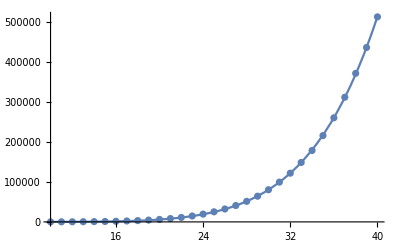

```mathematica
(* Basis size vs. Energy *)
x=Range[10,40];
y={116,186,293,460,706,1049,1590,2297,3261,4520,6170,8342,11157,14796,19471,25219,32287,40921,51419,64301,80421,99476,121851,148587,178643,215834,260320,311748,371498,436206,512821};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

{a→1.0934,b→2.92003}

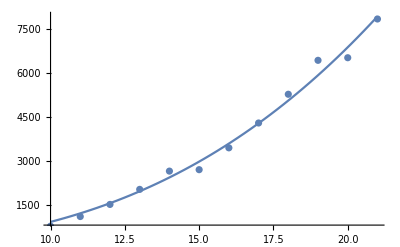

```mathematica
(* Number of operators vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={764,1093,1507,2022,2647,2696,3443,4293,5276,6437,6526,7851};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b*e/.{a->1.0933998100243698,b->2.920027336701123})
```

1.02136×10^7

{a→0.0000360917,b→7.79506}

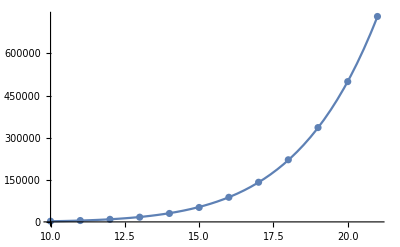

```mathematica
(* Nonzero matrix elements vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={2533,4869,9128,16819,30043,51342,87567,141158,221180,335805,499469,731377};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
(* size in bytes *)
(16*a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
```

2.61938×10^9

4.19101×10^10

```mathematica
(* Parametri relativi al generamento di VHH *)
```

```mathematica
data={
{21.0,29491,3530,1753,1.4356471139999998},{22.0,122411,4610,3775,3.1376362089999996},{23.0,271426,5461,6068,5.224180168},{24.0,474799,6510,8633,8.297623257000001},{25.0,731934,7696,11412,11.048218114000004},{26.0,1059434,8910,14600,14.528417628},{27.0,1455724,10256,18156,19.00853311600001},{28.0,1932711,11532,22171,24.330678196999997},{29.0,2472277,12951,26515,31.133256512000003},{30.0,3058154,14806,31006,46.288207016},{31.0,3734324,16700,35972,45.56107393899998},{32.0,4504708,18573,41398,56.951391626999964},{33.0,5393028,20452,47448,51.77494067500004},{34.0,6375648,22113,53964,55.65873874900001},{35.0,7414605,24536,60635,63.64368007799999},{36.0,8549129,27199,67689,79.29566364300001}
};
```

```mathematica
(* Number of non-zero matrix entries *)
nnz=data⟦All,{1,2}⟧
```

{{21.,29491},{22.,122411},{23.,271426},{24.,474799},{25.,731934},{26.,1059434},{27.,1455724},{28.,1932711},{29.,2472277},{30.,3058154},{31.,3734324},{32.,4504708},{33.,5393028},{34.,6375648},{35.,7414605},{36.,8549129}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→10452.,b→2.36538,c→-18.9689}

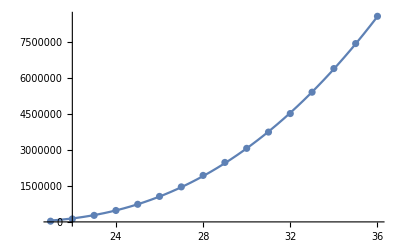

```mathematica
fit = FindFit[nnz, a*(z+c)^b,{a,b,c},z]
Show[Plot[a*(z+c)^b/.fit,{z,Min[nnz⟦All,1⟧],Max[nnz⟦All,1⟧]}],ListPlot[nnz]]
```

```mathematica
(* Estimate memory in bytes for sparse matrix *) 
a*(z+c)^b/.fit/.{z-> 60}
```

6.83642×10^7

```mathematica
(* size in MB *)
%*16/1000000
```

1093.83

```mathematica
(* Time spent to build the matrix *)
time=data⟦All,{1,5}⟧
zmin=20;
```

{{21.,1.43565},{22.,3.13764},{23.,5.22418},{24.,8.29762},{25.,11.0482},{26.,14.5284},{27.,19.0085},{28.,24.3307},{29.,31.1333},{30.,46.2882},{31.,45.5611},{32.,56.9514},{33.,51.7749},{34.,55.6587},{35.,63.6437},{36.,79.2957}}

{a→1.16172,b→1.50552}

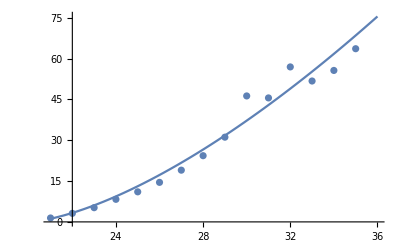

```mathematica
fit = FindFit[time, a*(z-zmin)^b,{a,b},z]
Show[Plot[a*(z-zmin)^b/.fit,{z,Min[time⟦All,1⟧],Max[time⟦All,1⟧]}],ListPlot[time]]
```

```mathematica
(* Estimated time spent to generate matrix *) 
a*(z-zmin)^b/.fit/.{z-> 60}
```

2663.35

```mathematica
(* in minutes *)
%/60
```

44.3892